# Billiards

```mathematica
Get[NotebookDirectory[]<>"../Kernel/init.m"] (*Load QuantumWalks package*)

Print["Last update: "<>DateString[{"Day"," ","MonthName"," ","Year"}]]
```

Last update: 25 February 2026

## Routines’ details and usage examples

## BuildShiftOperators[gridData,opts]

constructs the shift operators of a DTQW for a given grid geometry. These operators move the quantum walker between adjacent nodes while implementing unitary bounce-back boundary conditions—if the walker hits the edge of the billiard, it reflects into the opposite internal state to preserve the total probability.

For a grid provided via gridData, it returns the operators based on the chosen CoinDimension:

CoinDimension -> 2 (Default): Returns a list of two matrices {Sx, Sy} for a split-step quantum walk.

Sx: Horizontal conditional shift.

Sy: Vertical conditional shift.

CoinDimension -> 4: Returns a single global matrix S for a 4-coin-state DTQW.

Internal states are encoded as: 1:Up (+y), 2:Down (−y), 3:Right (+x), 4:Left (−x).

Note 1: All operators are returned as SparseArray objects to ensure high performance in large-scale simulations.

Note 2: gridData may be any other geometry with the same structure as that the output of functions Generate...Basis.

### Usage example

Constructing operators for a split-step walk on a Bunimovich stadium (L=10,R=15):

```mathematica
(*1. Generate the grid*)
BunimovichData=GenerateBunimovichBasis[10,15];

(*2. Build 2-state split-step operators (default)*)
{Sx,Sy}=BuildShiftOperators[BunimovichData];
```

The horizontal shift operator Sx structure:

```mathematica
(* Check the dimensions (2 states per spatial node) *)
Dimensions[Sx]

(* Verify that the operator is Unitary *)
UnitaryMatrixQ[Sx]
```

{706,706}

True

Constructing a single global operator for a 4-state walk:

```mathematica
(* Build 4-state Grover shift operator *)
SGlobal = BuildShiftOperators[BunimovichData, CoinDimension -> 4];

(* Check the dimensions (4 states per spatial node) *)
Dimensions[SGlobal]
```

{1412,1412}

Obtain the total number of non-zero entries to verify sparsity:

```mathematica
ArrayRules[SGlobal] // Length
```

1413

## GeneralizedGroverCoin[θ]

yields the 4×4 anisotropic Grover coin matrix 2*∣s(θ)⟩⟨s(θ)∣ - I_4, with ∣s(θ)⟩= 1/√2{cos(θ),cos(θ),sin(θ),sin(θ)}.

### Usage example

Generating a standard Grover coin (θ=π/4):

```mathematica
MatrixForm[GroverCoin=GeneralizedGroverCoin[Pi/4]]
```

(-1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | 1/2
1/2 | 1/2 | 1/2 | -1/2)

Verify GroverCoin is unitary:

```mathematica
(* Verify unitarity *)
UnitaryMatrixQ[GroverCoin]
(* Output: True *)
```

True

## BlockDiagonalCoin[ϕ]

yields a 4×4 block-diagonal rotation coin matrix:

### Usage example

Generating the block-diagonal coin with a ϕ=π/3:

```mathematica
MatrixForm[BlockDiagonalCoin[Pi/3]]
```

(1/2 | (ⅈ √3)/2 | 0 | 0
(ⅈ √3)/2 | 1/2 | 0 | 0
0 | 0 | 1/2 | (ⅈ √3)/2
0 | 0 | (ⅈ √3)/2 | 1/2)

## GeneralizedHadamardCoin[ξ]

yields the following 4×4 generalized Hadamard coin matrix:

### Usage example

Generating the coin with ξ=π/6:

```mathematica
MatrixForm[Chop[GeneralizedHadamardCoin[Pi/6]]]
```

((√(3/2))/2 | 1/(2 √2) | (√(3/2))/2 | 1/(2 √2)
1/(2 √2) | -(√(3/2))/2 | 1/(2 √2) | -(√(3/2))/2
(√(3/2))/2 | 1/(2 √2) | -(√(3/2))/2 | -1/(2 √2)
1/(2 √2) | -(√(3/2))/2 | -1/(2 √2) | (√(3/2))/2)

Confirm it is an SparseArray:

```mathematica
Head[HCoin]
```

SparseArray

## GenerateBunimovichBasis[l,R]

generates the coordinate basis and mapping for the desymmetrized (1/4) Bunimovich stadium using the boundary equations BoundaryX and BoundaryY. It selects integer points (m,n) that satisfy the stadium geometry constraints in the first quadrant.

For the desymmetrized Bunimovich billiard (reduced to 1/4 of its original size using spatial symmetries) with semi-length l and semi-circle radius R, it returns an Association object with the following keys:

“Coords”: A flat list with all valid spatial coordinates {x,y} that form the basis of the position Hilbert subspace.

“Mapping”: An Association object that acts as a dictionary. It allows entering a coordinate (e.g., {0,0}) and obtaining its corresponding matrix index in O(1) time.

“Dimension”: An integer indicating the total dimension of the spatial basis.

“Params”: A list with the original input parameters, saved as {semi-length l, semi-circle radius R}.

“Type”: The label “Bunimovich” to easily identify the generated geometry.

### Usage exmple

Coordinate basis and mapping for a desymmetrized Bunimovich stadium of semi-length l=10 and semi-circle radius R=15:

```mathematica
BunimovichData=GenerateBunimovichBasis[10,15];
```

The grid of BunimovichData:

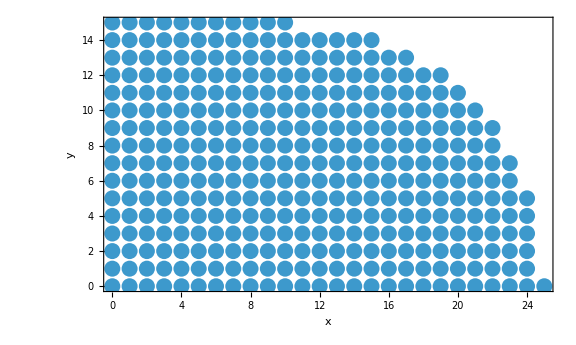

```mathematica
ListPlot[BunimovichData["Coords"],AspectRatio->Automatic,PlotStyle->Directive[PointSize[0.02]],Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x", "y"},ImageSize->Large]
```

Obtain the index of {5,10} in  BunimovichData[“Coords”]:

```mathematica
BunimovichData["Mapping"][{5,10}]
```

91

Obtain the number of points in  BunimovichData[“Coords”]:

```mathematica
BunimovichData["Dimension"]
```

353

Obtain the parameters {semi-length l, semi-circle R} of the data BunimovichData[“Coords”]:

```mathematica
BunimovichData["Params"]
```

{10,15}

Obtain the type of geometry of BunimovichData (in case the name you use to store the data is not suggestive):

```mathematica
BunimovichData["Type"]
```

Bunimovich

## GenerateFullStadiumBasis[L, R]

generates the coordinate basis and mapping for the full (non-desymmetrized) Bunimovich stadium. It iterates over a bounding box defined by the semi-length L and radius R , selecting integer points that fall within either the central rectangular region or the semicircular ends.

For the full Bunimovich stadium with semi-length L and radius R, it returns an Association object with the following keys:

"Coords" : A flat list with all valid spatial coordinates {x, y} that form the basis of the position Hilbert subspace .

"Mapping" : An Association object that acts as a dictionary . It allows entering a coordinate (e . g ., {0, 0}) and obtaining its corresponding matrix index in O (1) time .

"Dimension" : An integer indicating the total dimension of the spatial basis .

"Params" : An Association containing the original input parameters, saved as <|"L" -> L, "R" -> R, "Symmetry" -> "None"|> .

"Type" : The label "BunimovichFull" to identify the generated geometry .

### Usage example

Coordinate basis and mapping for a full Bunimovich stadium of semi-length L=10 and radius R=15:

```mathematica
FullStadiumData=GenerateFullStadiumBasis[10,15];
```

The grid of FullStadiumData:

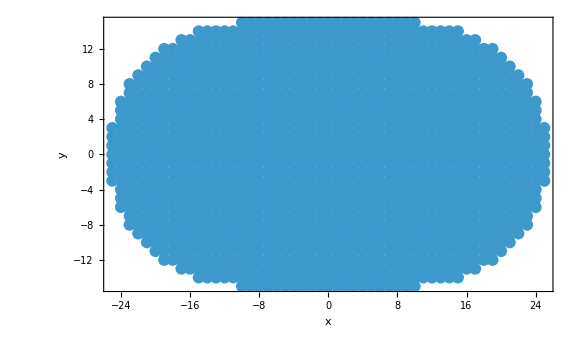

```mathematica
ListPlot[FullStadiumData["Coords"], 
 AspectRatio -> Automatic, 
 PlotStyle -> Directive[PointSize[0.015]], 
 Frame -> True, 
 FrameStyle -> Directive[Black, 20], 
 FrameLabel -> {"x", "y"}, 
 ImageSize -> Large]
```

Obtain the index of {0,15} (the top center point) in FullStadiumData:

```mathematica
FullStadiumData["Mapping"][{0,15}]
```

690

Obtain the total number of points in the full grid:

```mathematica
FullStadiumData["Dimension"]
```

1349

Obtain the parameters and symmetry metadata:

```mathematica
FullStadiumData["Params"]
```

<|L→10,R→15,Symmetry→None|>

Obtain the specific type of geometry:

```mathematica
FullStadiumData["Type"]
```

BunimovichFull

### Usage example